# Initialisation

```mathematica
Subscript[Y, ℓ_][θ_]=SphericalHarmonicY[ℓ,0,θ,ϕ];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}","\\definecolor{darkcyan}{RGB}{0, 180, 180}","\\definecolor{darkmagenta}{RGB}{180,0, 180}"}];
```

# Spherium: RHF, UHF and symmetry breaking

The general function for the Hartree-Fock energy is:

```mathematica
EHF[R_,λ_]=∑_(L=0)^1 Subscript[a, L]^2(L(L+1))/(2 R^2)+∑_(L=0)^1 Subscript[b, L]^2(L(L+1))/(2 R^2)+∑_(i=0)^1 ∑_(j=0)^1 ∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, i] Subscript[a, j] Subscript[b, k] Subscript[b, l] λ/R √((2i+1)(2j+1)(2k+1)(2l+1))∑_(L=0)^2 ThreeJSymbol[{i,0},{j,0},{L,0}]^2 ThreeJSymbol[{k,0},{l,0},{L,0}]^2/.{Subscript[a, 0]->Cos[x],Subscript[a, 1]->Sin[x],Subscript[b, 0]->Cos[y],Subscript[b, 1]->Sin[y]};
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
EHF[R,1]
```

(Cos[x]^2 Cos[y]^2)/R+Sin[x]^2/R^2+(Cos[y]^2 Sin[x]^2)/R+(4 Cos[x] Cos[y] Sin[x] Sin[y])/(3 R)+Sin[y]^2/R^2+(Cos[x]^2 Sin[y]^2)/R+(29 Sin[x]^2 Sin[y]^2)/(25 R)

We search stationnary solution

```mathematica
sol=Solve[{D[EHF[R,1], x]==0,D[EHF[R,1], y]==0},{x,y}]/.{C[1]->0,C[2]->0}//FullSimplify
```

{{x→0,y→0},{x→0,y→-π/2},{x→0,y→π/2},{x→0,y→π},{x→-π/2,y→0},{x→-π/2,y→-π/2},{x→-π/2,y→π/2},{x→-π/2,y→π},{x→π/2,y→0},{x→π/2,y→-π/2},{x→π/2,y→π/2},{x→π/2,y→π},{x→π,y→0},{x→π,y→-π/2},{x→π,y→π/2},{x→π,y→π},{x→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]}}

```mathematica
{D[EHF[R,1], x,x],D[EHF[R,1], y,y]}/.{x->0,y->-π/2}
```

{2/R^2+8/(25 R),-2/R^2}

Some solutions correspond to RHF solutions et some to UHF solutions.

```mathematica
solRHF={{x->0,y->0},{x->0,y->π},{x->-π/2,y->-π/2},{x->-π/2,y->π/2},{x->π/2,y->-π/2},{x->π/2,y->π/2},{x->π,y->0},{x->π,y->π},{x->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]}};
```

```mathematica
solUHF={{x->0,y->-π/2},{x->0,y->π/2},{x->-π/2,y->0},{x->-π/2,y->π},{x->π/2,y->0},{x->π/2,y->π},{x->π,y->-π/2},{x->π,y->π/2},{x->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]}};
```

The two electrons integrals are equal to

```mathematica
Subscript[U, i_,j_,k_,l_]:=√((2i+1)(2j+1)(2k+1)(2l+1))∑_(L=0)^2 ThreeJSymbol[{i,0},{j,0},{L,0}]^2 ThreeJSymbol[{k,0},{l,0},{L,0}]^2;
```

The Fock operator for the electron α is

```mathematica
Fα=Table[KroneckerDelta[i,j](i(i+1))/(2 R^2)+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, k] Subscript[a, l](Subscript[U, i,j,k,l]-Subscript[U, i,l,k,j])+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[b, k] Subscript[b, l](Subscript[U, i,j,k,l])/.{Subscript[a, 0]->Cos[x],Subscript[a, 1]->Sin[x],Subscript[b, 0]->Cos[y],Subscript[b, 1]->Sin[y]}/.λ->1//FullSimplify//Expand,{i,0,1},{j,0,1}]
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{{4/(3 R)-Cos[2 x]/(3 R),-Sin[2 x]/(3 R)+Sin[2 y]/(3 R)},{-Sin[2 x]/(3 R)+Sin[2 y]/(3 R),1/R^2+106/(75 R)+Cos[2 x]/(3 R)-(2 Cos[2 y])/(25 R)}}

And the Fock operator β

```mathematica
Fβ=Table[KroneckerDelta[i,j](i(i+1))/(2 R^2)+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[b, k] Subscript[b, l](Subscript[U, i,j,k,l]-Subscript[U, i,l,k,j])+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, k] Subscript[a, l](Subscript[U, i,j,k,l])/.{Subscript[a, 0]->Cos[x],Subscript[a, 1]->Sin[x],Subscript[b, 0]->Cos[y],Subscript[b, 1]->Sin[y]}/.λ->1//FullSimplify//Expand,{i,0,1},{j,0,1}]
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{{4/(3 R)-Cos[2 y]/(3 R),Sin[2 x]/(3 R)-Sin[2 y]/(3 R)},{Sin[2 x]/(3 R)-Sin[2 y]/(3 R),1/R^2+106/(75 R)-(2 Cos[2 x])/(25 R)+Cos[2 y]/(3 R)}}

## RHF solutions

In the RHF case Fα = Fβ

```mathematica
Fα/.solRHF//FullSimplify//Expand
```

{{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}}}

```mathematica
Fβ/.solRHF//FullSimplify//Expand
```

{{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}}}

The 16 stationnary RHF solutions yields 3  differents Fockian which are all diagonal.

```mathematica
{{{1/R,0},{0,1/R^2+5/(3 R)}}//MatrixForm,{{5/(3 R),0},{0,1/R^2+29/(25 R)}}//MatrixForm,{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}}//MatrixForm}
```

{(1/R | 0
0 | 1/R^2+5/(3 R)),(5/(3 R) | 0
0 | 1/R^2+29/(25 R)),(25/(44 R^2)+91/(66 R) | 0
0 | 25/(44 R^2)+91/(66 R))}

The first solution corresponds to a density matrix spatially symmetric where the two electrons are in Y_0 and the second to a density matrix spatially symmetric where the two electrons are in Y_1. The last solution corresponds to the symmetry broken RHF solution. In the sb-RHF solution the two orbitals are degenerate.

```mathematica
{D[EHF[R,1], x,x],D[EHF[R,1], y,y]}/.{{x->0,y->π},{x->π/2,y->-π/2},{x->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]}}//FullSimplify
```

{{2/R^2,2/R^2},{-(50+8 R)/(25 R^2),-(50+8 R)/(25 R^2)},{-4/(3 R),-4/(3 R)}}

```mathematica
Solve[-(50+8 R)/(25 R^2)==0,R]
```

{{R→-25/4}}

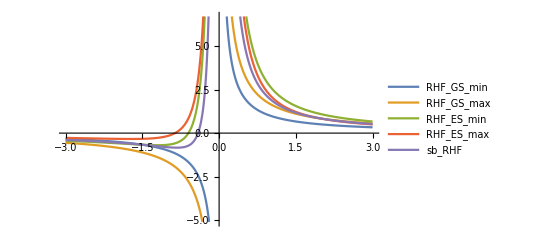

```mathematica
Plot[{1/R,5/(3R),1/R^2+5/(3 R),1/R^2+29/(25 R),25/(44 R^2)+91/(66 R)},{R,-3,3},PlotLegends->{"RHF_GS_min","RHF_GS_max","RHF_ES_min","RHF_ES_max","sb_RHF"}]
```

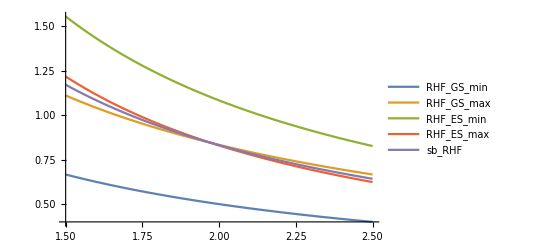

```mathematica
Plot[{1/R,5/(3R),1/R^2+5/(3 R),1/R^2+29/(25 R),25/(44 R^2)+91/(66 R)},{R,1.5,2.5},PlotLegends->{"RHF_GS_min","RHF_GS_max","RHF_ES_min","RHF_ES_max","sb_RHF"}]
```

```mathematica
Solve[5/(3 R)==1/R^2+29/(25 R),R]
```

{{R→75/38}}

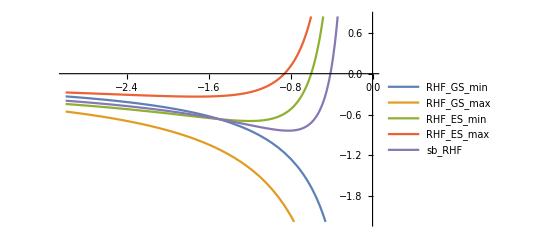

```mathematica
Plot[{1/R,5/(3R),1/R^2+5/(3 R),1/R^2+29/(25 R),25/(44 R^2)+91/(66 R)},{R,0,-3},PlotLegends->{"RHF_GS_min","RHF_GS_max","RHF_ES_min","RHF_ES_max","sb_RHF"}]
```

```mathematica
Solve[1/R==1/R^2+5/(3 R),R]
```

{{R→-3/2}}

The sb-RHF energy interacts with the minimized RHF for R<0 and the maximized RHF for R>0. For negative value of R there is a point at which the attraction of the sb-RHF will minimize the energy than the kinetical energy.  For positive value of lambda there is a point at which the repulsion of the sb RHF solution is bigger than the kinetical energy.

## UHF solutions

```mathematica
Fα/.solUHF//FullSimplify//Expand
```

{{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}}}

```mathematica
Fβ/.solUHF//FullSimplify//Expand
```

{{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}}}

The 16 stationnary UHF solutions yields 3  differents Fockian, only two of them are already diagonal.

```mathematica
{{{5/(3 R),0},{0,1/R^2+1/R}}//MatrixForm,{{1/R,0},{0,1/R^2+137/(75 R)}}//MatrixForm,DiagonalMatrix[{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}}//Eigenvalues//Expand]//MatrixForm}
```

{(5/(3 R) | 0
0 | 1/R^2+1/R),(1/R | 0
0 | 1/R^2+137/(75 R)),(25/(56 R^2)+57/(28 R) | 0
0 | 25/(56 R^2)+59/(84 R))}

```mathematica
{D[EHF[R,1], x,x],D[EHF[R,1], y,y]}/.{{x->0,y->π/2},{x->-π/2,y->0},{x->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]}}//FullSimplify
```

{{(50+8 R)/(25 R^2),-2/R^2},{-2/R^2,(50+8 R)/(25 R^2)},{4/(3 R),4/(3 R)}}

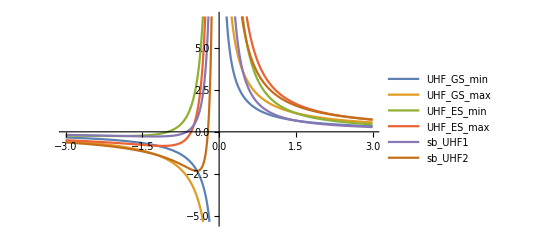

```mathematica
Plot[{1/R,5/(3R),1/R^2+1/R,1/R^2+137/(75 R),25/(56 R^2)+59/(84 R),25/(56 R^2)+57/(28 R)},{R,-3,3},PlotLegends->{"UHF_GS_min","UHF_GS_max","UHF_ES_min","UHF_ES_max","sb_UHF1","sb_UHF2"}]
```

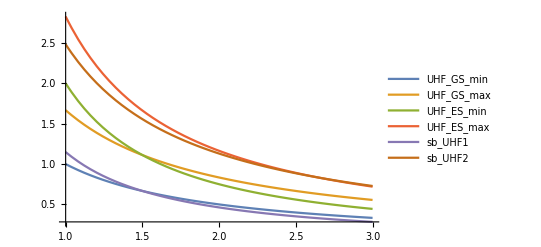

```mathematica
Plot[{1/R,5/(3R),1/R^2+1/R,1/R^2+137/(75 R),25/(56 R^2)+59/(84 R),25/(56 R^2)+57/(28 R)},{R,1,3},PlotLegends->{"UHF_GS_min","UHF_GS_max","UHF_ES_min","UHF_ES_max","sb_UHF1","sb_UHF2"}]
```

```mathematica
Solve[1/R^2+137/(75 R)==25/(56 R^2)+57/(28 R),R]
```

```mathematica
{{R->2325/878}}//N
```

{{R→2.64806}}

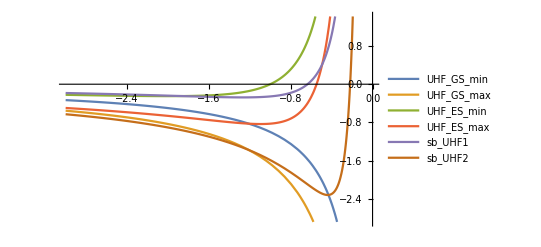

```mathematica
Plot[{1/R,5/(3R),1/R^2+1/R,1/R^2+137/(75 R),25/(56 R^2)+59/(84 R),25/(56 R^2)+57/(28 R)},{R,0,-3},PlotLegends->{"UHF_GS_min","UHF_GS_max","UHF_ES_min","UHF_ES_max","sb_UHF1","sb_UHF2"}]
```

For R>0 the sb-UHF solution is a minimum because the symmetry breaking minimize the repulsion and for R<0 this is a maximum because the symmetry breaking minimize the attraction.
For R>0 the sb-UHF 1 is the “bonding” solution and the sb-UHF 2 is the antibonding solution. There is a point a which the bonding solution becomes better than the ground state of the symmetric solution, and an other point at which the anti bonding solution becomes higher than the symetric solution.
We can do the same reasoning for R<0.

## sb-RHF and sb-UHF

### Coulson-Fischer points

```mathematica
Table[ EHF[R,1]/.sol⟦k⟧,{k,Length[sol]}]//FullSimplify//Expand//DeleteDuplicates
```

```mathematica
{1/R,1/R^2+1/R,2/R^2+29/(25 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R)}
```

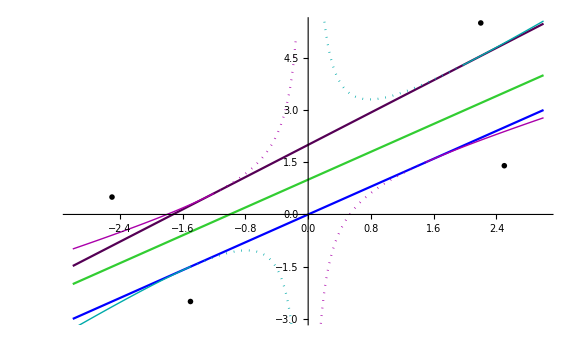

```mathematica
Show[Plot[{λ,1+λ,2+(29 λ)/25},{λ,-3,3},PlotStyle->{Blue,RGBColor["LimeGreen"],Darker[Purple]},PlotLegends->Placed[{MaTeX["\\text{s}^2",Magnification->1.5],MaTeX["\\text{sp}_\\text{z}",Magnification->1.5],MaTeX["\\text{p}_\\text{z}^2",Magnification->1.5]},{Left,Top}]],
Plot[25/28-75/(112 λ)+(59 λ)/84,{λ,3/2,3},PlotStyle->{Thick,Darker[Magenta]}],Plot[25/28-75/(112 λ)+(59 λ)/84,{λ,-75/62,3/2},PlotStyle->{Dotted,Darker[Magenta]}],Plot[25/28-75/(112 λ)+(59 λ)/84,{λ,-3,-75/62},PlotStyle->{Thick,Darker[Magenta]}],Plot[25/22+75/(88 λ)+(91 λ)/66,{λ,75/38,3},PlotStyle->{Thick,Darker[Cyan]}],Plot[25/22+75/(88 λ)+(91 λ)/66,{λ,-3/2,75/38},PlotStyle->{Dotted,Darker[Cyan]}],Plot[25/22+75/(88 λ)+(91 λ)/66,{λ,-3,-3/2},PlotStyle->{Thick,Darker[Cyan]}],
Epilog->{
Inset[MaTeX["\\text{\\textcolor{darkcyan}{sb-RHF state}}",Magnification->1.5],{2.2,5.5}],Inset[MaTeX["\\text{\\textcolor{darkmagenta}{sb-UHF state}}",Magnification->1.5],{2.5,1.4}],Inset[MaTeX["\\text{\\textcolor{darkcyan}{sb-RHF state}}",Magnification->1.5],{-1.5,-2.5}],Inset[MaTeX["\\text{\\textcolor{darkmagenta}{sb-UHF state}}",Magnification->1.5],{-2.5,0.5}]},
AxesLabel->{MaTeX["R",Magnification->1.5],MaTeX["E_\\text{HF}",Magnification->1.5]},AxesStyle->Directive[Thick,16],ImageSize->Large
]
```

```mathematica
EsHF[R_,λ_]=∑_(L=0)^1 Subscript[a, L]^2(L(L+1))/(2 R^2)+∑_(L=0)^1 Subscript[b, L]^2(L(L+1))/(2 R^2)+∑_(i=0)^1 ∑_(j=0)^1 ∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, i] Subscript[a, j] Subscript[b, k] Subscript[b, l] λ/R √((2i+1)(2j+1)(2k+1)(2l+1))∑_(L=0)^2 ThreeJSymbol[{i,0},{j,0},{L,0}]^2 ThreeJSymbol[{k,0},{l,0},{L,0}]^2/.{Subscript[a, 0]->-Sin[x],Subscript[a, 1]->Cos[x],Subscript[b, 0]->-Sin[y],Subscript[b, 1]->Cos[y]};
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
λ^2*Table[ EsHF[R,1]/.sol⟦k⟧,{k,Length[sol]}]/.R->λ//FullSimplify//Expand//DeleteDuplicates
```

{2+(29 λ)/25,1+λ,λ,13/22-225/(88 λ)+(2239 λ)/1650,37/28+225/(112 λ)+(1511 λ)/2100}

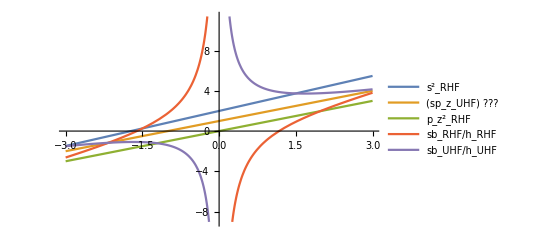

```mathematica
Plot[{2+(29 λ)/25,1+λ,λ,13/22-225/(88 λ)+(2239 λ)/1650,37/28+225/(112 λ)+(1511 λ)/2100},{λ,-3,3},PlotLegends->{"s^2_RHF","(sp_z_UHF) ???","p_z^2_RHF","sb_RHF/h_RHF","sb_UHF/h_UHF"}]
```

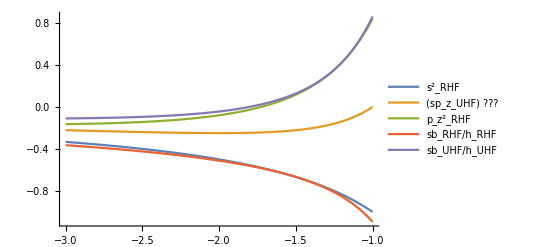

```mathematica
Plot[{1/R,1/R^2+1/R,2/R^2+29/(25 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R)},{R,-1,-3},PlotLegends->{"s^2_RHF","(sp_z_UHF) ???","p_z^2_RHF","sb_RHF/h_RHF","sb_UHF/h_UHF"}]
```

For R > 0:
-the sb_RHF solution is a maximum and exist for R>75/38 (~1.97) before it is a holomorphic solution
-the sb_UHF solution is a minimum and exist for R>3/2  before it is a holomorphic solution
For R<0:
-the sb_RHF solution is a minimum and exist for R<-3/2 after it is a holomorphic solution
-the sb_UHF solution is a maximum and exist for R<-75/62(~1.2) after it is a holomorphic solution

Those points are the Coulson-Fischer points of the sb-RHF and sb-UHF solutions.

## Mono electronic wavefunctions

```mathematica
Subscript[ϕ, HF]=(Cos[x]Subscript[Y, 0][θ1]+Sin[x]Subscript[Y, 1][θ1])(Cos[y]Subscript[Y, 0][θ2]+Sin[y]Subscript[Y, 1][θ2])
```

```mathematica
cα={{Cos[x],Sin[x]},{-Sin[x],Cos[x]}}ᵀ;	oα={{Cos[x]Subscript[Y, 0][θ1],Sin[x]Subscript[Y, 1][θ1]}}ᵀ;	Pα=oα.oαᵀ;
cβ={{Cos[y],Sin[y]},{-Sin[y],Cos[y]}}ᵀ;	oβ={{Cos[y]Subscript[Y, 0][θ2],Sin[y]Subscript[Y, 1][θ2]}}ᵀ;	Pβ=oβ.oβᵀ;
```

```mathematica
Pα+Pβ/.sol//FullSimplify
```

{{{1/(2 π),0},{0,0}},{{1/(4 π),0},{0,(3 Cos[θ2]^2)/(4 π)}},{{1/(4 π),0},{0,(3 Cos[θ2]^2)/(4 π)}},{{1/(2 π),0},{0,0}},{{1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{0,0},{0,(3 (Cos[θ1]^2+Cos[θ2]^2))/(4 π)}},{{0,0},{0,(3 (Cos[θ1]^2+Cos[θ2]^2))/(4 π)}},{{1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{0,0},{0,(3 (Cos[θ1]^2+Cos[θ2]^2))/(4 π)}},{{0,0},{0,(3 (Cos[θ1]^2+Cos[θ2]^2))/(4 π)}},{{1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{1/(2 π),0},{0,0}},{{1/(4 π),0},{0,(3 Cos[θ2]^2)/(4 π)}},{{1/(4 π),0},{0,(3 Cos[θ2]^2)/(4 π)}},{{1/(2 π),0},{0,0}},{{(-75+38 R)/(176 π R),(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(-75+38 R)/(176 π R),(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(-75+38 R)/(176 π R),-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(-75+38 R)/(176 π R),-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(-75+38 R)/(176 π R),-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(-75+38 R)/(176 π R),-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{-(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(-75+38 R)/(176 π R),(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(-75+38 R)/(176 π R),(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(704 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (-Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}},{{(75+62 R)/(224 π R),(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]-Cos[θ2]))/(448 π R),(75 (-3+2 R) (2+Cos[2 θ1]+Cos[2 θ2]))/(896 π R)}}}

```mathematica
Pα-Pβ/.sol//FullSimplify
```

{{{0,0},{0,0}},{{1/(4 π),0},{0,-(3 Cos[θ2]^2)/(4 π)}},{{1/(4 π),0},{0,-(3 Cos[θ2]^2)/(4 π)}},{{0,0},{0,0}},{{-1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{0,0},{0,(3 (Cos[2 θ1]-Cos[2 θ2]))/(8 π)}},{{0,0},{0,(3 (Cos[2 θ1]-Cos[2 θ2]))/(8 π)}},{{-1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{-1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{0,0},{0,(3 (Cos[2 θ1]-Cos[2 θ2]))/(8 π)}},{{0,0},{0,(3 (Cos[2 θ1]-Cos[2 θ2]))/(8 π)}},{{-1/(4 π),0},{0,(3 Cos[θ1]^2)/(4 π)}},{{0,0},{0,0}},{{1/(4 π),0},{0,-(3 Cos[θ2]^2)/(4 π)}},{{1/(4 π),0},{0,-(3 Cos[θ2]^2)/(4 π)}},{{0,0},{0,0}},{{0,(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (-Cos[θ1]+Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R)},{(5 √(9+6 R) √(-75+38 R) (Cos[θ1]-Cos[θ2]))/(352 π R),(75 (3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(704 π R)}},{{0,(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}},{{0,(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}},{{0,-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}},{{0,-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}},{{0,-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}},{{0,-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{-(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}},{{0,(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}},{{0,(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R)},{(5 √(-9+6 R) √(75+62 R) (Cos[θ1]+Cos[θ2]))/(448 π R),(75 (-3+2 R) (Cos[2 θ1]-Cos[2 θ2]))/(896 π R)}}}

```mathematica
(Cos[x]Subscript[Y, 0][θ1]+Sin[x]Subscript[Y, 1][θ1])/.x->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]//FullSimplify
```

(√(75+62 R)+5 √(-9+6 R) Cos[θ1])/(8 √(7 π) √R)

```mathematica
{(Cos[x]Subscript[Y, 0][θ1]+Sin[x]Subscript[Y, 1][θ1]),(-Sin[x]Subscript[Y, 0][θ1]+Cos[x]Subscript[Y, 1][θ1])}/.{x->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]}//FullSimplify
```

{(√(-75+38 R)-5 √(9+6 R) Cos[θ1])/(4 √(22 π) √R),(5 √(3+2 R)+√3 √(-75+38 R) Cos[θ1])/(4 √(22 π) √R)}

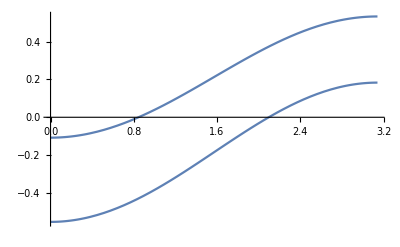

```mathematica
Plot[{-(√(-75+38 R)+5 √(9+6 R) Cos[θ1])/(4 √(22 π) √R),-(-5 √(3+2 R)+√3 √(-75+38 R) Cos[θ1])/(4 √(22 π) √R)}/.R->1000,{θ1,0,π}]
```

```mathematica
EHF[R_,λ_]=∑_(L=0)^1 Subscript[a, L]^2(L(L+1))/(2 R^2)+∑_(L=0)^1 Subscript[b, L]^2(L(L+1))/(2 R^2)+∑_(i=0)^1 ∑_(j=0)^1 ∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, i] Subscript[a, j] Subscript[b, k] Subscript[b, l] λ/R √((2i+1)(2j+1)(2k+1)(2l+1))∑_(L=0)^2 ThreeJSymbol[{i,0},{j,0},{L,0}]^2 ThreeJSymbol[{k,0},{l,0},{L,0}]^2/.{Subscript[a, 0]->Cos[x],Subscript[a, 1]->Sin[x],Subscript[b, 0]->Cos[y],Subscript[b, 1]->Sin[y]}/.λ->1/.sol//FullSimplify//Expand
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{1/R,1/R^2+1/R,1/R^2+1/R,1/R,1/R^2+1/R,2/R^2+29/(25 R),2/R^2+29/(25 R),1/R^2+1/R,1/R^2+1/R,2/R^2+29/(25 R),2/R^2+29/(25 R),1/R^2+1/R,1/R,1/R^2+1/R,1/R^2+1/R,1/R,75/(88 R^3)+25/(22 R^2)+91/(66 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R)}

```mathematica
EHF[R_,λ_]=∑_(L=0)^1 Subscript[a, L]^2(L(L+1))/(2 R^2)+∑_(L=0)^1 Subscript[b, L]^2(L(L+1))/(2 R^2)+∑_(i=0)^1 ∑_(j=0)^1 ∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, i] Subscript[a, j] Subscript[b, k] Subscript[b, l] λ/R √((2i+1)(2j+1)(2k+1)(2l+1))∑_(L=0)^2 ThreeJSymbol[{i,0},{j,0},{L,0}]^2 ThreeJSymbol[{k,0},{l,0},{L,0}]^2/.{Subscript[a, 0]->-Sin[x],Subscript[a, 1]->Cos[x],Subscript[b, 0]->-Sin[y],Subscript[b, 1]->Cos[y]}/.λ->1/.sol//FullSimplify//Expand
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{2/R^2+29/(25 R),1/R^2+1/R,1/R^2+1/R,2/R^2+29/(25 R),1/R^2+1/R,1/R,1/R,1/R^2+1/R,1/R^2+1/R,1/R,1/R,1/R^2+1/R,2/R^2+29/(25 R),1/R^2+1/R,1/R^2+1/R,2/R^2+29/(25 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),-225/(88 R^3)+13/(22 R^2)+2239/(1650 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R),225/(112 R^3)+37/(28 R^2)+1511/(2100 R)}

## Singularity structure

```mathematica
{Subscript[ψα, 1][θ_,R_]:=Cos[χα]Subscript[Y, 0][θ]+Sin[χα]Subscript[Y, 1][θ]/.χα->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],
Subscript[ψβ, 1][θ_,R_]:=Cos[χβ]Subscript[Y, 0][θ]+Sin[χβ]Subscript[Y, 1][θ]/.χβ->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],
Subscript[ψα, 2][θ_,R_]:=-Sin[χα]Subscript[Y, 0][θ]+Cos[χα]Subscript[Y, 1][θ]/.χα->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],
Subscript[ψβ, 2][θ_,R_]:=-Sin[χβ]Subscript[Y, 0][θ]+Cos[χβ]Subscript[Y, 1][θ]/.χβ->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]}//FullSimplify;
```

```mathematica
{Ψ1=Subscript[ψα, 1][θ1,R]Subscript[ψβ, 1][θ2,R],Ψ2=Subscript[ψα, 1][θ1,R]Subscript[ψβ, 2][θ2,R],Ψ3=Subscript[ψα, 2][θ1,R]Subscript[ψβ, 1][θ2,R],Ψ4=Subscript[ψα, 2][θ1,R]Subscript[ψβ, 2][θ2,R]}//FullSimplify;
```

```mathematica
S[Ψ1_,Ψ2_,R_]:=(2π)^2∫_0^π ∫_0^π Expand[Ψ1 Ψ2] Sin[θ1]Sin[θ2]ⅆθ1ⅆθ2//FullSimplify
H[Ψ1_,Ψ2_,R_]:=(2π)^2/(2 R^2)∫_0^π ∫_0^π Expand[(D[Ψ1, θ1])(D[Ψ2, θ1])+(D[Ψ1, θ2])(D[Ψ2, θ2])]Sin[θ1]Sin[θ2]ⅆθ1ⅆθ2+(2π)^2/R∫_0^π ∫_0^π Expand[Ψ1 Ψ2(1+Cos[θ1] Cos[θ2]+1/4 (-1+3 Cos[θ1]^2) (-1+3 Cos[θ2]^2))] Sin[θ1]Sin[θ2]ⅆθ1ⅆθ2//FullSimplify
```

```mathematica
H[Ψ1,Ψ1,R]
```

(225+4 R (75+91 R))/(264 R^3)

```mathematica
({{H[Ψ1,Ψ1,R], H[Ψ2,Ψ1,R], H[Ψ3,Ψ1,R], H[Ψ4,Ψ1,R]}, {H[Ψ1,Ψ2,R], H[Ψ2,Ψ2,R], H[Ψ3,Ψ2,R], H[Ψ4,Ψ2,R]}, {H[Ψ1,Ψ3,R], H[Ψ2,Ψ3,R], H[Ψ3,Ψ3,R], H[Ψ4,Ψ3,R]}, {H[Ψ1,Ψ4,R], H[Ψ2,Ψ4,R], H[Ψ3,Ψ4,R], H[Ψ4,Ψ4,R]}})
```

```mathematica
{{(225+4 R (75+91 R))/(264 R^3),0,0,(75+4 R (3+R))/(88 R^3)},{0,(225+4 R (75+47 R))/(264 R^3),(75+4 R (3+R))/(88 R^3),(√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3)},{0,(75+4 R (3+R))/(88 R^3),(225+4 R (75+47 R))/(264 R^3),(√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3)},{(75+4 R (3+R))/(88 R^3),(√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3),(√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3),(-16875+4 R (975+2239 R))/(6600 R^3)}}//MatrixForm
```

```mathematica
sbRHF[R_]:=({{(225+4 R (75+91 R))/(264 R^3), 0, 0, (75+4 R (3+R))/(88 R^3)}, {0, (225+4 R (75+47 R))/(264 R^3), (75+4 R (3+R))/(88 R^3), (√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3)}, {0, (75+4 R (3+R))/(88 R^3), (225+4 R (75+47 R))/(264 R^3), (√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3)}, {(75+4 R (3+R))/(88 R^3), (√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3), (√(3+2 R) (25+2 R) √(-75+38 R))/(220 R^3), (-16875+4 R (975+2239 R))/(6600 R^3)}})
```

On veut vérifier f^α ψ^α = ϵ ψ^α

```mathematica
h(1)ψ^α= -1/2 D[ψ^α, θ,θ]
```

```mathematica
Subscript[ψα, 1][θ_,R_]:=Cos[χα]Subscript[Y, 0][θ]+Sin[χα]Subscript[Y, 1][θ]/.χα->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]
```

```mathematica
∑_a^(N^α) [Subscript[J, a]^α(1)-Subscript[K, a]^α(1)]+∑_a^(N^β) Subscript[J, a]^β(1)
```

Ici un seul électron α et un seul β

```mathematica
Subscript[J, a]^α(1)=∫Subscript[ψ, a]^SuperStar[α](2)1/Subscript[r, 12] Subscript[ψ, a]^α(2)ⅆ Subscript[r, 2]
```

```mathematica
Subscript[ψα, 1][θ1,R]//FullSimplify
```

(√(-75+38 R)+5 √(9+6 R) Cos[θ1])/(4 √(22 π) √R)

```mathematica
-1/(2 R^2 Sin[θ1])D[(Sin[θ1]D[Subscript[ψα, 1][θ1,R], θ1]), θ1]//FullSimplify
```

```mathematica
(5 √(9+6 R) Cos[θ1])/(4 √(22 π) R^(5/2))=1/R^2 (5 √(9+6 R) Cos[θ1])/(4 √(22 π) √R)
```

```mathematica
Subscript[ψα, 2][θ1,R]//FullSimplify
```

(-5 √(3+2 R)+√3 √(-75+38 R) Cos[θ1])/(4 √(22 π) √R)

```mathematica
-1/(2 R^2 Sin[θ1])D[(Sin[θ1]D[Subscript[ψα, 2][θ1,R], θ1]), θ1]//FullSimplify
```

```mathematica
(√(3/(22 π)) √(-75+38 R) Cos[θ1])/(4 R^(5/2))=1/R^2 (√3 √(-75+38 R) Cos[θ1])/(4 √(22 π) √R)
```

```mathematica
(2π R^2)/R∫_0^π Subscript[ψα, 1][θ2,R](1+Cos[θ1] Cos[θ2]+1/4 (-1+3 Cos[θ1]^2) (-1+3 Cos[θ2]^2))Subscript[ψα, 1][θ2,R]Sin[θ2]ⅆθ2
```

```mathematica
1/528 (20 √(9+6 R) √(-75+38 R) Cos[θ1]+9 (5+62 R+5 (3+2 R) Cos[2 θ1]))Subscript[ψα, 1][θ1,R]+(5 √(9+6 R) Cos[θ1])/(4 √(22 π) R^(5/2))//FullSimplify
```

(66 R^2 (15+26 R) √(-75+38 R)+5 √(9+6 R) (1056+5 R^2 (-75+302 R)) Cos[θ1]+15 R^2 (3+2 R) (26 √(-75+38 R) Cos[2 θ1]+15 √(9+6 R) Cos[3 θ1]))/(4224 √(22 π) R^(5/2))

```mathematica
1/528 (20 √(9+6 R) √(-75+38 R) Cos[θ1]+9 (5+62 R+5 (3+2 R) Cos[2 θ1]))
```

```mathematica
Subscript[K, a]^α(1)Subscript[ψ, i]^α(1)=[∫Subscript[ψ, a]^SuperStar[α](2)1/Subscript[r, 12] Subscript[ψ, i]^α(2)ⅆ Subscript[r, 2]] Subscript[ψ, a]^α(1)
```

```mathematica
1/Subscript[r, 12]=(1+Cos[θ1] Cos[θ2]+1/4 (-1+3 Cos[θ1]^2) (-1+3 Cos[θ2]^2))
```